```mathematica
dataUpTo7=Import[FileNameJoin[{NotebookDirectory[],"data",ToString[#]}]][[All,3;;4]]&/@Range[2,7]
```

```mathematica
plotFacetVert[data_,dim_]:=Show[Plot[(2^(dim+1)×dim)/x,{x,1,2^(dim+1)},PlotRange->All,PlotStyle->{LightBlue,Dashed}],ListPlot[data,PlotStyle->{PointSize[0.01],Yellow},AxesOrigin->{0,0}],PlotRange->{{0,2^dim+2},{0,2^dim+2}},AspectRatio->1,AxesOrigin->{0,0},AxesStyle->{{Bold,White},{Bold,White}},AxesLabel->(Style[#,White,Background->Black]&/@{"Facets","Vertices"}),GridLines->Automatic,GridLinesStyle->Gray,Background->Black,PlotLabel->Style["Facets and vertices of 2-level polytopes in dim "<>ToString[dim],White,Background->Black],ImageSize->600]
```

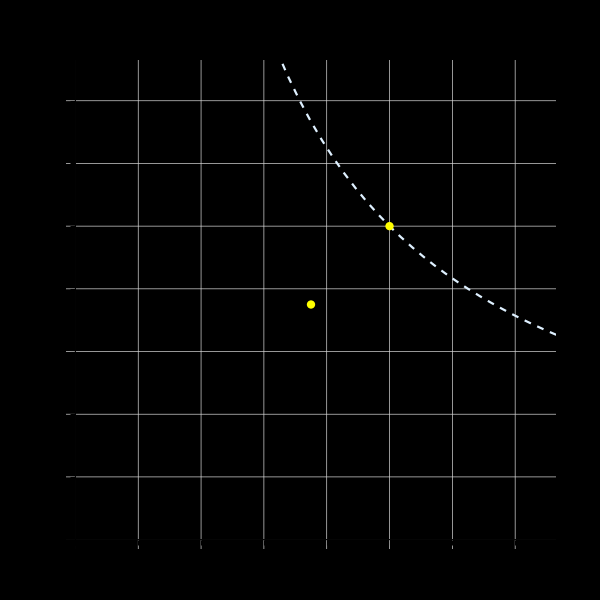
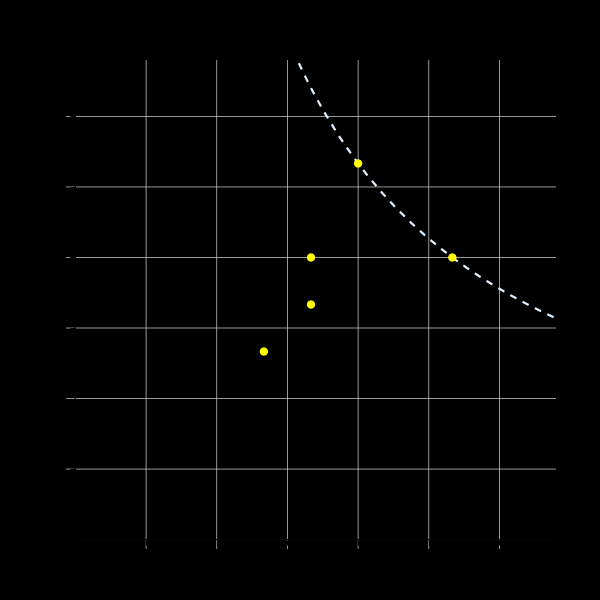
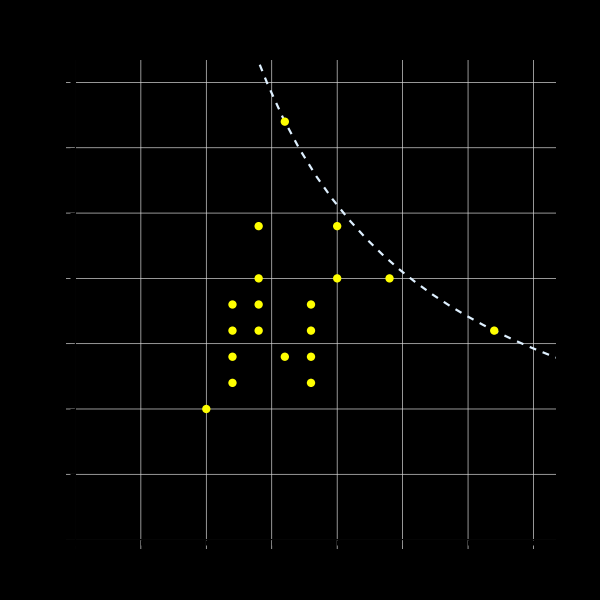
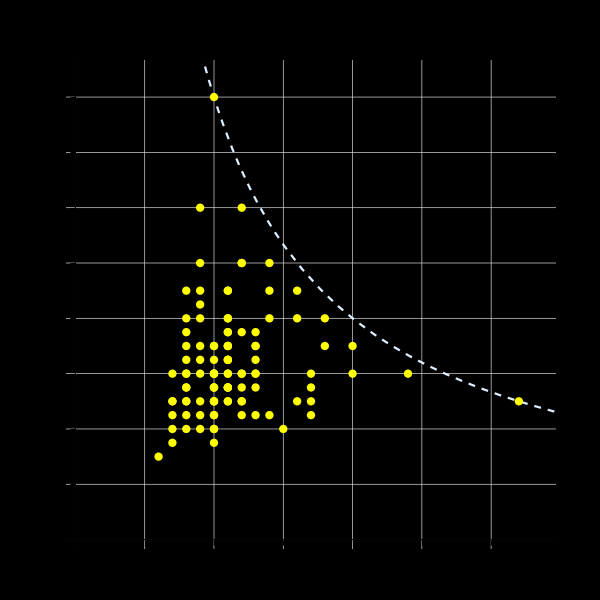
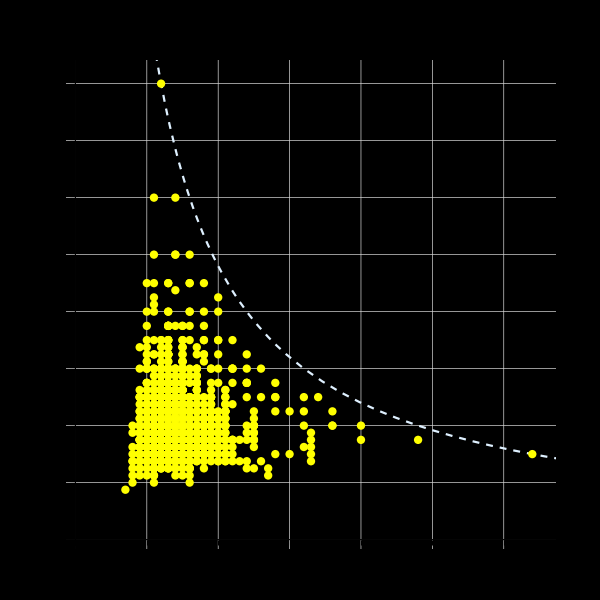
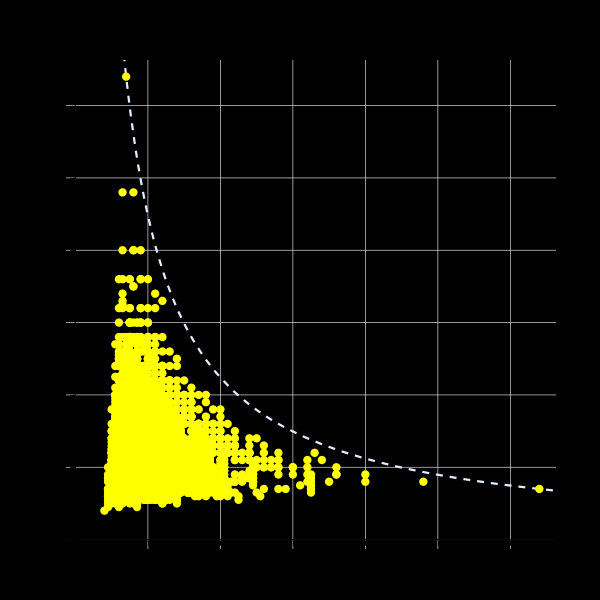

```mathematica
MapIndexed[plotFacetVert[#1,#2[[1]]+1]&,dataUpTo7]
```

```mathematica
MapIndexed[Export[FileNameJoin[{NotebookDirectory[],"2level-vert-facet-plots-"<>ToString[#2[[1]]+1]<>".jpg"}],#1]&,%];
```

```mathematica
points8=Import[FileNameJoin[{NotebookDirectory[],"data","8-points.csv"}]];
```

```mathematica
plotFacetVert[points8,8]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"2level-vert-facet-plots-8.jpg"}],%];
```